```mathematica
(*[a,b], x z [[a,b], k-il miejsc po przecinku*)
```

```mathematica
zamianaRB[a_,b_,x_,k_]:=Module[{int, frac,re,n,m,p,q},
n=Max[
Length[IntegerDigits[a,2]],
Length[IntegerDigits[b,2]]];(*ilosc miejsc na czesci calkowiej*)
m=Length[IntegerDigits[10^k,2]];
(*calkowitych tyle ile najwieksza z przedzialu, po przecinku ile zadane w k*)
(*Kazdy dopelnia do n, po przecinku do k i zwraca jako ciag dl n+k*)
p=IntegerDigits[IntegerPart[x],2,n];(*calkowita wartosc*)
q=IntegerDigits[10^k*Round[FractionalPart[x],10^-k],2,m];
(*czesc ulamkowa*)
Join[p,q]
]
```

```mathematica
(* [a,b], liczba binarna {0,0,1...} k- ilość miejsc po przecinku*)
```

```mathematica
zamianaBR[a_,b_,x_,k_]:=Module[{n,m,p,q,int,frac},
n=Max[
Length[IntegerDigits[a,2]],
Length[IntegerDigits[b,2]]];
m=Length[IntegerDigits[10^k,2]];
(*Print["x: ",x];
Print[pocz];*)
(*czesc calkowita binarnie*)
p=Table[0,{n}];
For[i=1,i<n,i++,p⟦i⟧=x⟦i⟧];
(*czesc niecalkowita binarnie*)
q=Table[0,{m}];
For[i=1,i<m,i++,q⟦i⟧=x⟦i+n⟧];
(*Print["n: ",n,", m:",m, " p: ",p, " q: ",q, " x : ",x];*)
int=FromDigits[p,2];
frac=(10^-k)*FromDigits[q,2];
(*Print["w: ",int+frac*1.];
Print[kon];*)
int+frac*1.

]
```

## PBIL na rzeczywistych

```mathematica
Clear[pbil,newP,valuate,compare];
(*funkcja zliczająca jedynki*)
valuate[x_]:=Module[{val=0, n= Length[x],i=0,j=0,k=0},
For[i=1,i≤n,i++,val+= x⟦i⟧];
val];
(*n-dł osobnika, λ-współczynnik uczenia się, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm na przedziale [a,b], dokl miejsc po przecinku*)
pbilRE[λ_,f_,size_,maxT_,itmax_,a_,b_,dokl_]:=Module[{aBin,bBin,P,best,population, n,max=maxT[[2]],k,iter=1,wynik=Table[{0,0},{1}]},
n=Max[
Length[IntegerDigits[a,2]],
Length[IntegerDigits[b,2]]];
k=Length[IntegerDigits[10^dokl,2]];
population=Table[Table[0,{n+k}],{size}];
P=Table[0.5,{n+k}];
aBin=zamianaRB[a,b,a,dokl];
bBin=zamianaRB[a,b,b,dokl];
(*generacja pop startowej*)
SeedRandom[];
(*Porównywanie wartości funkcji dla osobników*)
compare[x1_,y_]:=If[
(f/.x->(zamianaBR[a,b,x1,dokl]))>(f/.x->(zamianaBR[a,b,y,dokl])),x1,y];
(*gdy przekroczy przedzial przyjmuje skrajna wartosc*)
przytnij[x_]:=
If[(zamianaBR[a,b,x,dokl])>b,bBin, 
If[(zamianaBR[a,b,x,dokl])<a,aBin,x]
];

For[j=1,j≤size,j++,
For[i=1,i≤n+k,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
];
population⟦j⟧=przytnij[population⟦j⟧]
];
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
(*Print["best:",best," //",population⟦1⟧];*)
(*Algorytm kończy działanie po osiągnięciu max albo ilości iteracji*)
Print["_______________________________"];
While[((f/.x->(zamianaBR[a,b,best,dokl]))≠max  && iter≠itmax),
(*wyszukiwanie najlepszego osobnika*)

For[i=1,i≤size,i++,best=compare[population⟦i⟧,best]];

(*Print["best:",zamianaBR[a,b,best,dokl]," iter: ",iter];*)
wynik⟦iter⟧={iter,f/.x->(zamianaBR[a,b,best,dokl])};
(*Obliczenie nowego wektora prawdopodobienstwa*)
For[i=1,i≤n+k,i++,P⟦i⟧=(1-λ) P⟦i⟧+λ best⟦i⟧];
(*Generacja nowej populacji*)
For[j=1,j≤size,j++,
For[i=1,i≤n+k,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
];
population⟦j⟧=przytnij[population⟦j⟧]
];

iter++;
wynik2=Table[{iter,f/.x->(zamianaBR[a,b,best,dokl])},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];

Print["Maximum (",zamianaBR[a,b,best,dokl],", ",f/.x->zamianaBR[a,b,best,dokl],"), (rzeczywiste: ",maxT,") uzyskane po iteracjach: ",iter];

(*Print[wynik];*)
ListLinePlot[wynik]
]
```

(*λ, f, size, max, iter, a, b, dokl*)
(-(x-2)^2)

PBIL dla -(x-2)^2 na [0,20] dokładność 10^-4, populacja 20os, wsp uczenia 0.1, max 200it

_______________________________

Maximum (0.894, -1.22324), (rzeczywiste: {2,0}) uzyskane po iteracjach: 200

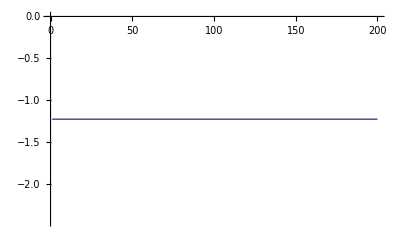

```mathematica
pbilRE[0.1,-(x-2)^2,5,{2,0},200,0,20,4]
```

PBIL dla -(x-2)^2 na [0,20] dokładność 10^-2, populacja 20os, wsp uczenia 0.1, max 200it

_______________________________

Maximum (3.2, -1.44), (rzeczywiste: {2,0}) uzyskane po iteracjach: 200

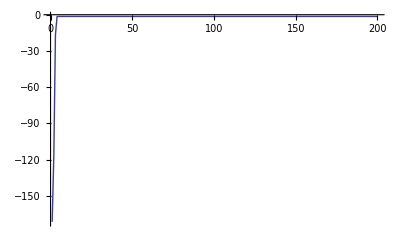

```mathematica
pbilRE[0.1,-(x-2)^2,5,{2,0},200,0,20,2]
```

PBIL dla -(x-2)^2 na [0,20] dokładność 10^-4, populacja 20os, wsp uczenia 0.01, max 200it

_______________________________

Maximum (2.4088, -0.167117), (rzeczywiste: {2,0}) uzyskane po iteracjach: 200

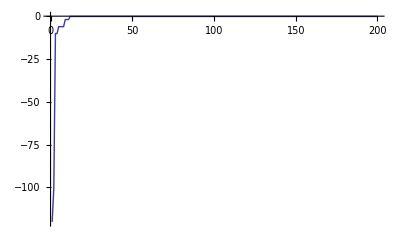

```mathematica
pbilRE[0.01,-(x-2)^2,5,{2,0},200,0,20,4]
```

PBIL dla -(x-2)^2 na [0,20] dokładność 10^-4, populacja 20os, wsp uczenia 0.01, max 100it

_______________________________

Maximum (2.3944, -0.155551), (rzeczywiste: {2,0}) uzyskane po iteracjach: 100

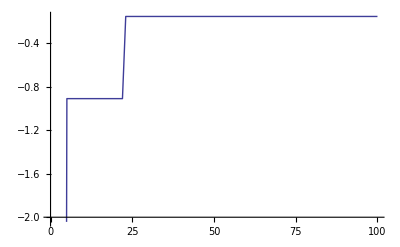

```mathematica
pbilRE[0.01,-(x-2)^2,5,{2,0},100,0,20,4]
```

PBIL dla -(x-2)^2 na [0,5] dokładność 10^-4, populacja 20os, wsp uczenia 0.01, max 200it

_______________________________

Maximum (2.1896, -0.0359482), (rzeczywiste: {2,0}) uzyskane po iteracjach: 200

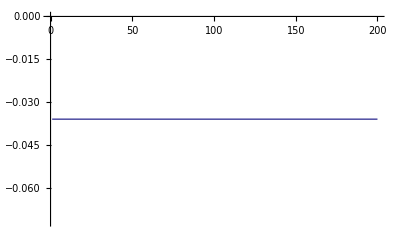

```mathematica
pbilRE[0.01,-(x-2)^2,5,{2,0},200,0,5,4]
```

PBIL dla x na [0,5] dokładność 10^-1, populacja 5os, wsp uczenia 0.01, max 200it

```mathematica
pbilRE[0.01,x,5,{5,5},200,0,5,1]
```

_______________________________

$Aborted

## PBIL na rzeczywistych + zatrzymanie po q tych samych osobnikach

```mathematica
Clear[pbil,newP,valuate,compare];
(*funkcja zliczająca jedynki*)
valuate[x_]:=Module[{val=0, n= Length[x],i=0,j=0,k=0},
For[i=1,i≤n,i++,val+= x⟦i⟧];
val];
(*n-dł osobnika, λ-współczynnik uczenia się, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm na przedziale [a,b], dokl miejsc po przecinku*)
pbilREq[λ_,f_,size_,maxT_,itmax_,a_,b_,dokl_,qmax_]:=Module[{aBin,bBin,P,best,oldbest,population, n,max=maxT[[2]],k,iter=1, q=0,wynik=Table[{0,0},{1}]},
n=Max[
Length[IntegerDigits[a,2]],
Length[IntegerDigits[b,2]]];
k=Length[IntegerDigits[10^dokl,2]];
population=Table[Table[0,{n+k}],{size}];
P=Table[0.5,{n+k}];
aBin=zamianaRB[a,b,a,dokl];
bBin=zamianaRB[a,b,b,dokl];
(*generacja pop startowej*)
SeedRandom[];
(*Porównywanie wartości funkcji dla osobników*)
compare[x1_,y_]:=If[
(f/.x->(zamianaBR[a,b,x1,dokl]))>(f/.x->(zamianaBR[a,b,y,dokl])),x1,y];
(*gdy przekroczy przedzial przyjmuje skrajna wartosc*)
przytnij[x_]:=
If[(zamianaBR[a,b,x,dokl])>b,bBin, 
If[(zamianaBR[a,b,x,dokl])<a,aBin,x]
];

For[j=1,j≤size,j++,
For[i=1,i≤n+k,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
];
population⟦j⟧=przytnij[population⟦j⟧]
];
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
(*Algorytm kończy działanie po osiągnięciu max albo ilości iteracji*)
While[((f/.x->(zamianaBR[a,b,best,dokl]))≠max  && iter≠itmax&&qmax≠ q),
(*wyszukiwanie najlepszego osobnika*)
oldbest=best;
For[i=1,i≤size,i++,best=compare[population⟦i⟧,best]];
If[oldbest==best,q++,q=0];
wynik⟦iter⟧={iter,f/.x->(zamianaBR[a,b,best,dokl])};
(*Obliczenie nowego wektora prawdopodobienstwa*)
For[i=1,i≤n+k,i++,P⟦i⟧=(1-λ) P⟦i⟧+λ best⟦i⟧];
(*Generacja nowej populacji*)
For[j=1,j≤size,j++,
For[i=1,i≤n+k,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
];
population⟦j⟧=przytnij[population⟦j⟧]
];

iter++;
wynik2=Table[{iter,f/.x->(zamianaBR[a,b,best,dokl])},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];

Print["Maximum (",zamianaBR[a,b,best,dokl],", ",f/.x->zamianaBR[a,b,best,dokl],"), (rzeczywiste: ",maxT,") uzyskane po iteracjach: ",iter];
punkt={zamianaBR[a,b,best,dokl],f/.x->zamianaBR[a,b,best,dokl]};
(*Print[wynik];*)
Print[Show[Plot[f,{x,a,b}],ListPlot[{punkt},Filling->Axis,PlotStyle->Red]]];
Print[punkt];
ListLinePlot[wynik,PlotLabel->"Zbieżność do max"]
]
```

```mathematica
(*λ, f, size, max, iter, a, b, dokl,max powtarzajacych sie max*)
```

(-(x-2)^2)

PBIL dla -(x-2)^2 na [0,20] dokładność 10^-4, populacja
 5os, wsp uczenia 0.01, max 100it, max 20 tych samych osobników

Maximum (2.4412, -0.194657), (rzeczywiste: {2,0}) uzyskane po iteracjach: 29

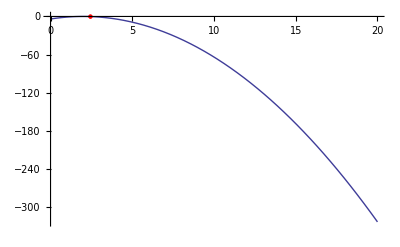

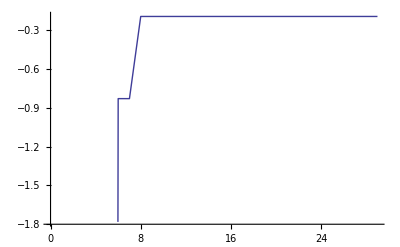

```mathematica
pbilREq[0.01,-(x-2)^2,5,{2,0},100,0,20,4,20]
```

PBIL dla -(x-2)^2 na [0,20] dokładność 10^-6, populacja
5os, wsp uczenia 0.01, max 100it, max 130 tych samych osobników

Maximum (2.79004, -0.624163), (rzeczywiste: {2,0}) uzyskane po iteracjach: 100

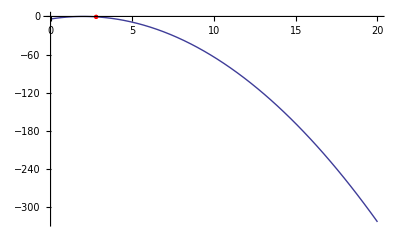

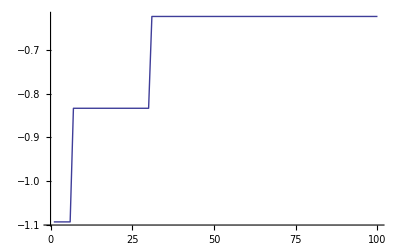

```mathematica
pbilREq[0.01,-(x-2)^2,5,{2,0},100,0,20,6,130]
```

PBIL dla -(x-2)^2 na [0,5] dokładność 10^-6, populacja
5os, wsp uczenia 0.01, max 200it, max 130 tych samych osobników

Maximum (2.08694, -0.00755891), (rzeczywiste: {2,0}) uzyskane po iteracjach: 133

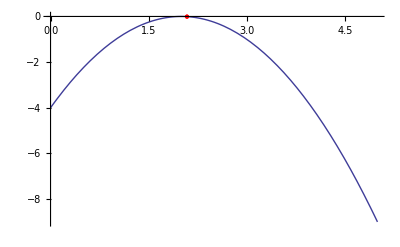

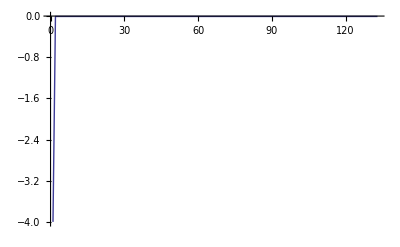

```mathematica
pbilREq[0.01,-(x-2)^2,5,{2,0},200,0,5,6,130]
```

sin (x)

PBIL dla Sin(x) na [0,π] dokładność 10^-3, populacja
 5os, wsp uczenia 0.001, max 200it, max 130 tych samych osobników

Maximum (2.054, 0.885511), (rzeczywiste: {1.5708,1}) uzyskane po iteracjach: 200

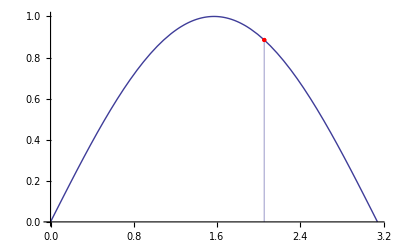

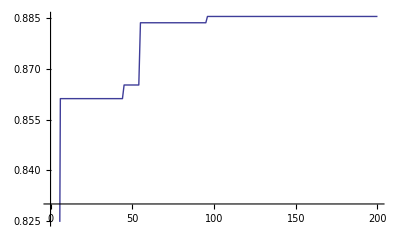

```mathematica
pbilREq[0.001,Sin[x],5,{π/2.,1},200,0,π,3,130]
```

PBIL dla Sin(x) na [0,π] dokładność 10^-5, populacja
 5os, wsp uczenia 0.001, max 200it, max 130 tych samych osobników

Maximum (1.29816, 0.963064), (rzeczywiste: {1.5708,1}) uzyskane po iteracjach: 171

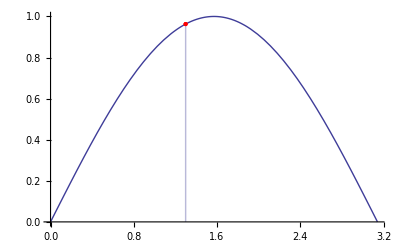

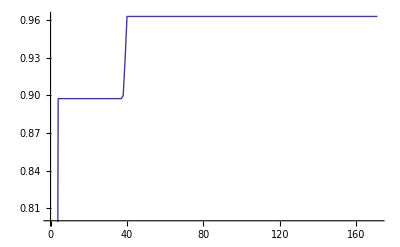

```mathematica
pbilREq[0.001,Sin[x],5,{π/2.,1},200,0,π,5,130]
```

PBIL dla Sin(x) na [0,π] dokładność 10^-5, populacja
 15os, wsp uczenia 0.001, max 200it, max 130 tych samych osobników

Maximum (1.31058, 0.966334), (rzeczywiste: {1.5708,1}) uzyskane po iteracjach: 200

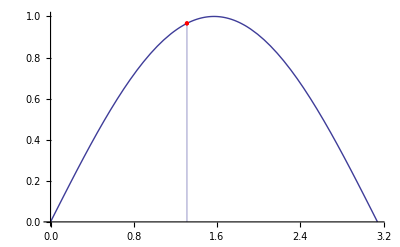

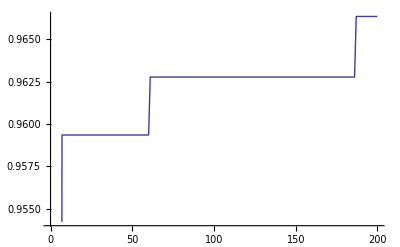

```mathematica
pbilREq[0.001,Sin[x],15,{π/2.,1},200,0,π,5,130]
```

PBIL dla Sin(x) na [0,π] dokładność 10^-6, populacja
 20os, wsp uczenia 0.001, max 200it, max 130 tych samych osobników

Maximum (2.00009, 0.909258), (rzeczywiste: {1.5708,1}) uzyskane po iteracjach: 170

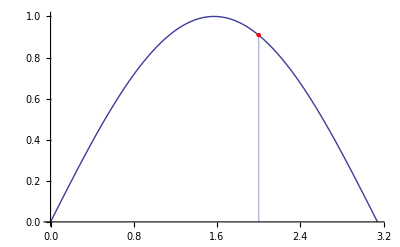

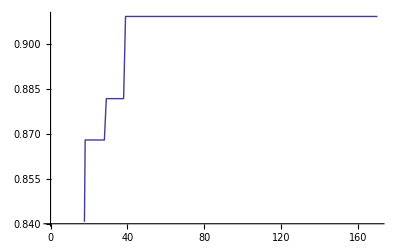

```mathematica
pbilREq[0.001,Sin[x],5,{π/2.,1},300,0,π,6,130]
```

test1 (x)

test1(x)=sin(x)+|x|

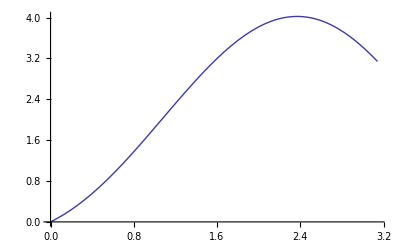

```mathematica
test1[x_]:=Abs[x]*Sin[x]+Abs[x];
Plot[test1[x],{x,0,π}]
```

PBIL dla test1(x) na [0,π] dokładność 10^-6, populacja
 10os, wsp uczenia 0.001, max 200it, max 130 tych samych osobników

Maximum (2.3693, 4.02255), (rzeczywiste: {2.5,4}) uzyskane po iteracjach: 212

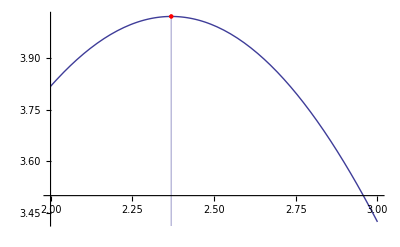

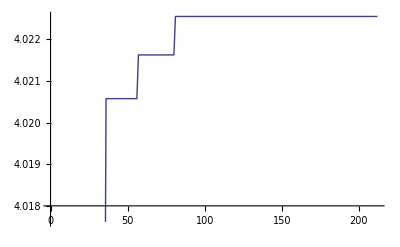

```mathematica
pbilREq[0.001,test1[x],10,{2.5,4},300,2,3,6,130]
```

test2 (x)

test2(x)=|x| sin(x) + 1/10 x

```mathematica
P2=FindMaximum[test2[x],{x,0,π}]
```

{2.02442,{x→2.06531}}

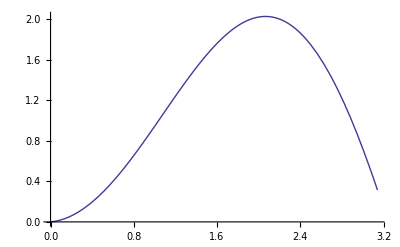

```mathematica
test2[x_]:=Abs[x]*Sin[x]+1/10 x;
Plot[test2[x],{x,0,Pi}]
```

PBIL dla test2(x) na [0,π] dokładność 10^-6, populacja
 10os, wsp uczenia 0.001, max 200it, max 130 tych samych osobników

Maximum (2.06241, 2.0244), (rzeczywiste: {2.06531,2.02442}) uzyskane po iteracjach: 186

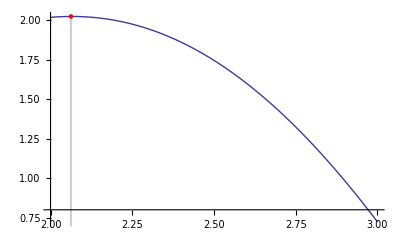

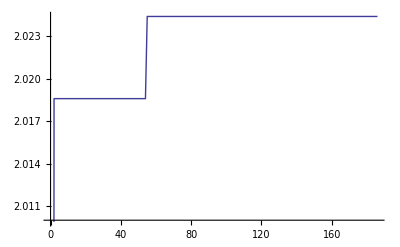

```mathematica
pbilREq[0.001,test2[x],10,{P2[[2,1,2]],P2[[1]]},200,2,3,6,130]
```

PBIL dla test2(x) na [0,π] dokładność 10^-4, populacja
 10os, wsp uczenia 0.01, max 200it, max 130 tych samych osobników

Maximum (2., 2.01859), (rzeczywiste: {2.06531,2.02442}) uzyskane po iteracjach: 133

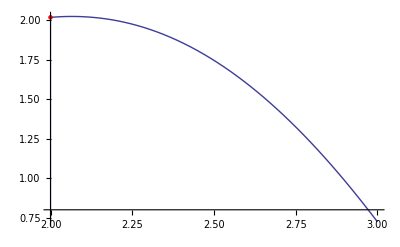

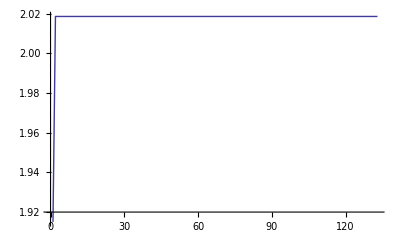

```mathematica
pbilREq[0.01,test2[x],10,{P2[[2,1,2]],P2[[1]]},200,2,3,4,130]
```

test3 (x)

test3[x_] := Module[{},
  If[0 <= x <= 2.773, -(x - 1)^2 + 2, -6 (x - 4)^2 + 8]]

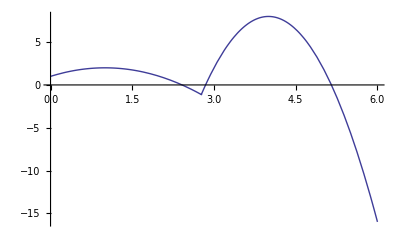

```mathematica
test3[x_]:=Module[{},If[0≤x≤2.773,-(x-1)^2+2,-6 (x-4)^2+8]];
Plot[test3[x],{x,0,6}]
```

```mathematica
P3={8.,{x->4.000000000011882}}(*FindMaximum[-6 (x-4)^2+8,{x,3,6}]*)
```

{8.,{x→4.}}

PBIL dla test3(x) na [0,6] dokładność 10^-4, populacja
 10os, wsp uczenia 0.01, max 200it, max 130 tych samych osobników

Maximum (4.0158, 7.9985), (rzeczywiste: {4.,8.}) uzyskane po iteracjach: 145

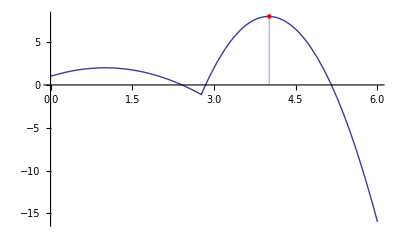

{4.0158,7.9985}

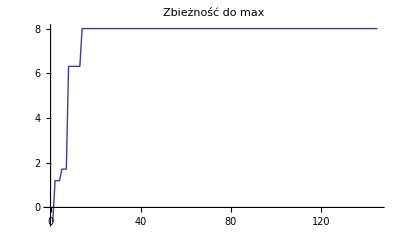

```mathematica
pbilREq[0.01,test3[x],10,{P3[[2,1,2]],P3[[1]]},200,0,6,4,130]
```

PBIL dla test3(x) na [0,6] dokładność 10^-4, populacja
 10os, wsp uczenia 0.001, max 200it, max 130 tych samych osobników

Maximum (4.0036, 7.99992), (rzeczywiste: {4.,8.}) uzyskane po iteracjach: 200

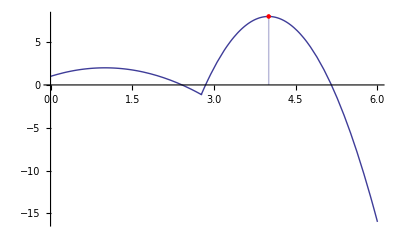

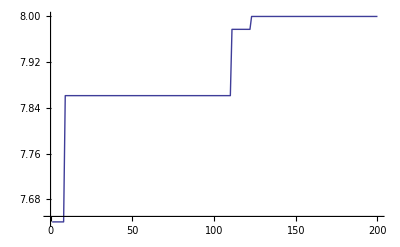

```mathematica
pbilREq[0.001,test3[x],10,{P3[[2,1,2]],P3[[1]]},200,0,6,4,130]
```

PBIL dla test3(x) na [0,6] dokładność 10^-4, populacja
 10os, wsp uczenia 0.001, max 300it, max 130 tych samych osobników

Maximum (4.0652, 7.97449), (rzeczywiste: {4.,8.}) uzyskane po iteracjach: 168

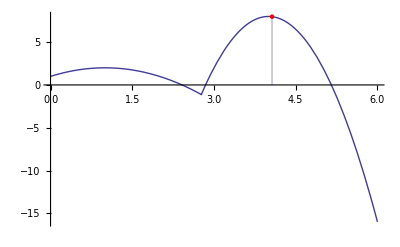

{4.0652,7.97449}

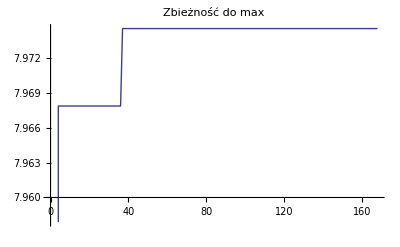

```mathematica
pbilREq[0.001,test3[x],10,{P3[[2,1,2]],P3[[1]]},300,0,6,4,130]
```

```mathematica
test4(x)
```

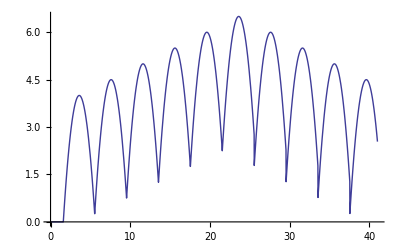

```mathematica
fi[i_]:=-1(x-3.6-4*i)^2+4+i*.5;(*i=0,4*)
fj[i_]:=-1(x-3.6-4*i)^2+6.5-(Mod[i,5])*.5;(*i,5,9*)
test4[w_]:=Module[{n=43/80,g=0},
If[1.6≤ w≤ 5+n,g=fi[0],
If[5+n≤ w≤ 9+n,g=fi[1],
If[9+n≤ w≤13+n,g=fi[2],
If[13+n≤ w≤ 17+n,g=fi[3],
If[17+n≤ w≤ 21+n,g=fi[4],
If[21+n≤ w≤ 25+n,g=fj[5],
If[25+n≤ w≤ 29+n,g=fj[6],
If[29+n≤ w≤ 33+n,g=fj[7],
If[33+n≤ w≤ 37+n,g=fj[8],
If[37+n≤ w≤41+n,g=fj[9],
g=0;
]]]]]]]]]];
g/.x->w];
Plot[test4[x],{x,0,41}]
```

```mathematica
P4=FindMaximum[fi[4],{x,17,21}]
```

{6.,{x→19.6}}

```mathematica
test5(x)
```

```mathematica
test5[x_]:=-(x-5)^2+Cos[18Pi (x-5)]+25
```

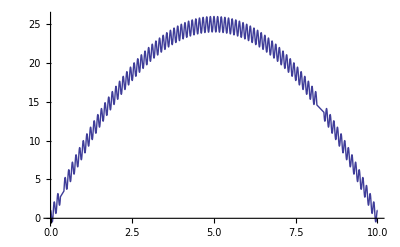

```mathematica
Plot[test5[x],{x,0,10},AxesOrigin->{0,0}]
```

PBIL dla test5(x) na [0,10] dokładność 10^-4, populacja
 10os, wsp uczenia 0.001, max 300it, max 40 tych samych osobników

Maximum (4.8776, 25.7881), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 61

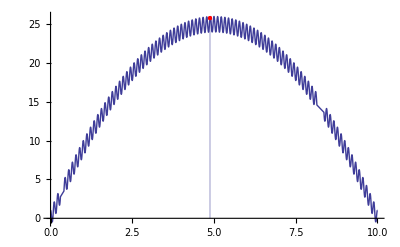

{4.8776,25.7881}

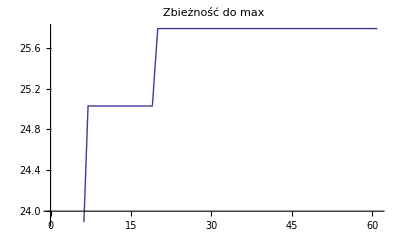

```mathematica
pbilREq[0.001,test5[x],10,{5.,26},300,0,10,4,40]
```

PBIL dla test5(x) na [0,10] dokładność 10^-4, populacja
 30os, wsp uczenia 0.001, max 300it, max 400 tych samych osobników

Maximum (4.9012, 25.7575), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 67

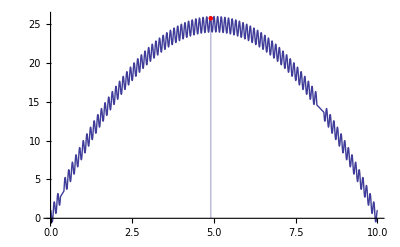

{4.9012,25.7575}

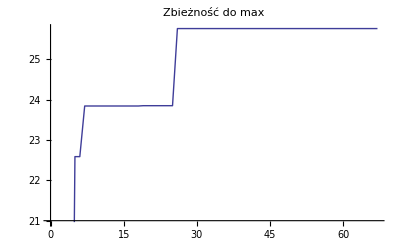

```mathematica
pbilREq[0.001,test5[x],10,{5.,26},300,0,10,4,40]
```

PBIL dla test5(x) na [0,10] dokładność 10^-4, populacja
 30os, wsp uczenia 0.01, max 300it, max 400 tych samych osobników

Maximum (5.3318, 25.8862), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 85

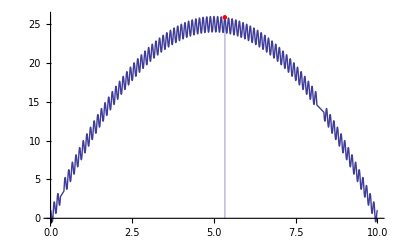

{5.3318,25.8862}

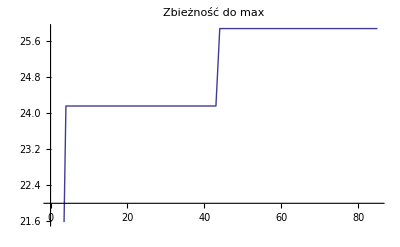

```mathematica
pbilREq[0.01,test5[x],10,{5.,26},300,0,10,4,40]
```

PBIL dla test5(x) na [0,10] dokładność 10^-4, populacja
 30os, wsp uczenia 0.1, max 300it, max 400 tych samych osobników

Maximum (6.3518, 23.6752), (rzeczywiste: {5.,26}) uzyskane po iteracjach: 44

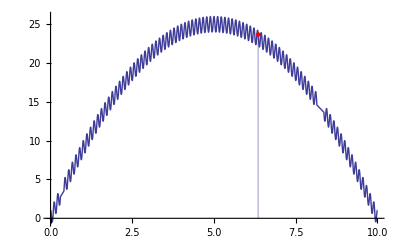

{6.3518,23.6752}

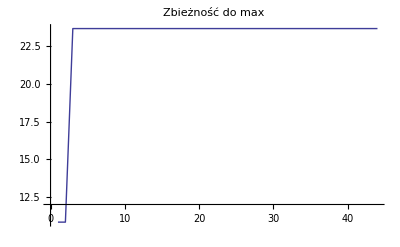

```mathematica
pbilREq[0.1,test5[x],10,{5.,26},300,0,10,4,40]
```